```mathematica
PHASE SPACE 
No of phase space variables: positions (x) + momenta(p) = 2n=10
No of constants of motion = n
No of actions(momenta)  = n
No of angle(positions)      = n
n = 5 for spinning BBHs.
```

```mathematica
Phase space variables: R, P, S1, S2
L = R x P;   J = L +S1+S2

===========================CONSTANTS OF MOTION AND ACTION VARIABLES

C = {H,|L|, |J|, Jz, L.Seff};Seff = σ1 S1+σ2 S2
J={J1, J2, J3, J4, J5};      J(C)

===========================
SEPARATRIX CRITERION
|C/J| = 0
5x 5 matrix Jacobian: |(J(C))/C| :=f(C)= ∞.
In 1D: dC/dJ = 0    < ==>  dJ/dC = ∞.
```

```mathematica
===========================
HOW TO FIND THE SEPARATRIX: EXAMPLE
```

```mathematica
f(C) = L/(L-1/H) =∞
g(C) = L-1/H  = 0   < ==>  L = 1/H
```

```mathematica
Plot[ 1/H, {H,0,1}, AxesLabel->{H,L}]
```

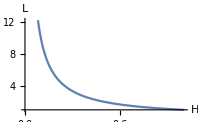
```mathematica
-Graphics-
How to land close to g(C) =0? 
Choose a random point. Compute ∇g ==> gives you direction of maximum decrease/increase of g.
```

```mathematica
===========================
1. Evolution equations for R, P, S1, S2
2. J(C) for |dJ/dC| = ∞.
```